# Funciones MOP dadas por R:

### Distribución Normal

```mathematica
(*Muestra de la distribución Normal(0,1)*)
```

```mathematica
SeedRandom[1234]
```

```mathematica
data1= RandomVariate[NormalDistribution[0,1],10001]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9973,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

```mathematica
data=Delete[data1,7615]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9972,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

```mathematica
(*DENSIDAD MOP DE GRADO 11 DADA POR R*)
```

```mathematica
f11R[x_]=0.399848459057202-0.0134715403688568*x-0.190752716237083*x^2+0.00748552600302952*x^3+0.0386171845628472*x^4-0.00156990693527791*x^5-0.00396403240321359*x^6+0.000156742654560431*x^7+0.000201132192265087*x^8-(7.50760685203839*^-6)*x^9-(3.98400008780918*^-6)*x^10+(1.3885489399642*^-7)*x^11
```

0.399848-0.0134715 x-0.190753 x^2+0.00748553 x^3+0.0386172 x^4-0.00156991 x^5-0.00396403 x^6+0.000156743 x^7+0.000201132 x^8-7.50761×10^-6 x^9-3.984×10^-6 x^10+1.38855×10^-7 x^11

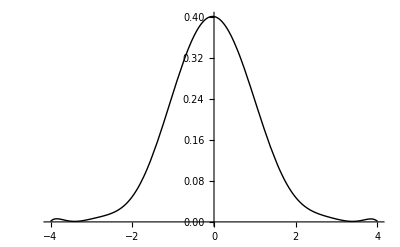

```mathematica
Plot[f11R[x],{x,-4,4},PlotStyle->{Black,Thin}]
```

```mathematica
(*Divergencia KL*)
```

```mathematica
N[Integrate[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

0.999937

```mathematica
F[x_]=(PDF[NormalDistribution[0,1],x])/0.9999366575163338
```

0.398968 ⅇ^(-x^2/2)

```mathematica
KLR11= N[Integrate[F[x]*Log[F[x]/f11R[x]],{x,-4,4}]]
```

0.00360385

```mathematica
(*BIC*)
```

```mathematica
x11R = Log[f11R[data]]
```

{-1.02448,-0.916673,-2.19705,-2.16839,-4.383,-1.75937,-1.48083,-0.931245,-0.925361,-2.34095,-0.918485,-0.936239,-1.37578,-1.22509,9972,-1.12472,-1.03883,-1.5575,-0.961427,-1.5165,-1.24568,-0.954734,-1.54032,-0.919912,-1.51459,-1.54504,-0.98749,-1.39495,-0.975756}
 |  |  |  |

```mathematica
V11R= Apply[Plus,x11R]
```

-14179.2

```mathematica
BICR11 = -2*V11R+ 12*Log[10000]
```

28468.9

```mathematica
(*DENSIDAD MOP DE GRADO 13 DADA POR R*)
```

```mathematica
f13R[x_]=0.400719284921557-0.00971456620957568*x-0.196070541577297*x^2-0.000897119885495176*x^3+0.0432401275237906*x^4+0.00323286598938725*x^5-0.00532657635543814*x^6-0.000952132969912304*x^7+0.000377582967941978*x^8+0.000113293431762736*x^9-(1.43755777533892*^-5*x^10)-(6.08598711396329*^-6)*x^11+(2.27639908275456*^-7)*x^12+(1.22454977891157*^-7)*x^13
```

0.400719-0.00971457 x-0.196071 x^2-0.00089712 x^3+0.0432401 x^4+0.00323287 x^5-0.00532658 x^6-0.000952133 x^7+0.000377583 x^8+0.000113293 x^9-0.0000143756 x^10-6.08599×10^-6 x^11+2.2764×10^-7 x^12+1.22455×10^-7 x^13

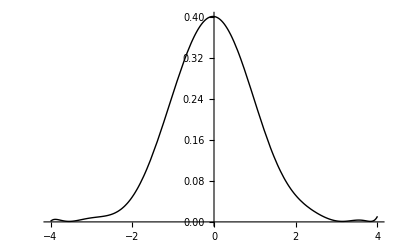

```mathematica
Plot[f13R[x],{x,-4,4},PlotStyle->{Black,Thin}]
```

```mathematica
(*Divergencia KL*)
```

```mathematica
KLR13= N[Integrate[F[x]*Log[F[x]/f13R[x]],{x,-4,4}]]
```

0.00345784

```mathematica
(*BIC*)
```

```mathematica
x13R = Log[f13R[data]]
```

{-1.02777,-0.915218,-2.1821,-2.16763,-4.56794,-1.75149,-1.47953,-0.92801,-0.922349,-2.32584,-0.915987,-0.932879,-1.38211,-1.22834,9972,-1.12425,-1.04232,-1.56725,-0.963161,-1.52567,-1.24869,-0.951184,-1.54984,-0.917261,-1.51251,-1.54226,-0.984102,-1.40173,-0.977974}
 |  |  |  |

```mathematica
V13R= Apply[Plus,x13R]
```

-14178.7

```mathematica
BICR13 = -2*V13R+ 14*Log[10000]
```

28486.3

### Distribución Chi Cuadrado

```mathematica
(*Muestra de la distribución chi cuadrado con 5 g.l.*)
```

```mathematica
SeedRandom[4321]
```

```mathematica
datos=RandomVariate[ChiSquareDistribution[5],10^4]
```

{3.92611,2.34812,4.86475,5.40946,9.92656,2.7506,9988,5.97406,3.2106,6.68792,2.10678,2.86916,1.42768}
 |  |  |  |

```mathematica
(*DENSIDAD MOP GRADO 6 DADA POR R*)
```

```mathematica
f6R[x_]=0.000999999999999979+0.115723709018987*x-0.0308715035966202*x^2+0.0032684442438179*x^3-0.000171162611337162*x^4+(4.42896274801922*^-6)*x^5-(4.52978219818507*^-8)*x^6
```

0.001+0.115724 x-0.0308715 x^2+0.00326844 x^3-0.000171163 x^4+4.42896×10^-6 x^5-4.52978×10^-8 x^6

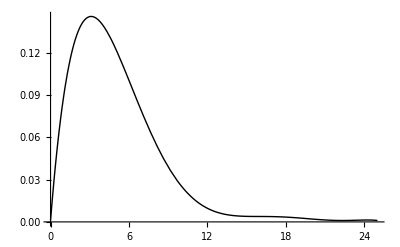

```mathematica
Plot[f6R[x],{x,0,25},PlotStyle->{Black,Thin}]
```

```mathematica
(*Divergencia KL*)
```

```mathematica
N[Integrate[PDF[ChiSquareDistribution[5],x],{x,0,25}]]
```

0.999861

```mathematica
G[x_]=(PDF[ChiSquareDistribution[5],x])/0.9998606662088144
```

1.00014 (Piecewise[{{(ⅇ^(-x/2) x^(3/2))/(3 √(2 π)), x>0}, {0, True}}])

```mathematica
KLR6= N[Integrate[G[x]*Log[G[x]/f6R[x]],{x,0,25}]]
```

0.011781

```mathematica
(*BIC*)
```

```mathematica
x6R = Log[f6R[datos]]
```

{-1.96199,-1.96655,-2.07735,-2.17312,-3.63581,-1.93351,-2.20509,-1.99983,-1.9262,-1.96375,-1.92642,-1.93189,-2.39729,-2.29241,9972,-1.93068,-1.93539,-2.11464,-2.23059,-1.93651,-1.95374,-1.97068,-1.98232,-2.29215,-1.92577,-2.46963,-2.00136,-1.92876,-2.1882}
 |  |  |  |

```mathematica
V6R= Apply[Plus,x6R]
```

-24407.6

```mathematica
BICR6 = -2*V6R+ 6*Log[10000]
```

48870.4

```mathematica
(*DENSIDAD MOP GRADO 12 DADA POR R*)
```

```mathematica
f12R[x_]=0.000999999999999969+0.0655888214956996*x+0.0369243972074178*x^2-0.0311968870919998*x^3+0.00925746509874915*x^4-0.00160393945925864*x^5+0.000183618226093193*x^6-(1.44812519854242*^-5)*x^7+(7.91995688494042*^-7)*x^8-(2.9496848832021*^-8)*x^9+(7.13119894904339*^-10)*x^10-(1.0080753736351*^-11)*x^11+(6.31907521844256*^-14)*x^12
```

0.001+0.0655888 x+0.0369244 x^2-0.0311969 x^3+0.00925747 x^4-0.00160394 x^5+0.000183618 x^6-0.0000144813 x^7+7.91996×10^-7 x^8-2.94968×10^-8 x^9+7.1312×10^-10 x^10-1.00808×10^-11 x^11+6.31908×10^-14 x^12

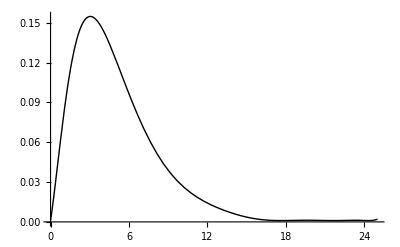

```mathematica
Plot[f12R[x],{x,0,25},PlotStyle->{Black,Thin}]
```

```mathematica
(*Divergencia KL*)
```

```mathematica
N[Integrate[PDF[ChiSquareDistribution[5],x],{x,0,25}]]
```

0.999861

```mathematica
G[x_]=(PDF[ChiSquareDistribution[5],x])/0.9998606662088144
```

1.00014 (Piecewise[{{(ⅇ^(-x/2) x^(3/2))/(3 √(2 π)), x>0}, {0, True}}])

```mathematica
KLR12= N[Integrate[G[x]*Log[G[x]/f12R[x]],{x,0,25}]]
```

0.00408045

```mathematica
(*BIC*)
```

```mathematica
x12R = Log[f12R[datos]]
```

{-1.92366,-1.9147,-2.07631,-2.19404,-3.55514,-1.87381,-2.23204,-1.9582,-1.86642,-1.92614,-1.86658,-1.87925,-2.44948,-2.33302,9972,-1.87068,-1.87597,-2.11246,-2.26965,-1.87727,-1.91193,-1.92003,-1.95188,-2.33272,-1.86849,-2.52707,-1.96022,-1.86869,-2.21221}
 |  |  |  |

```mathematica
V12R= Apply[Plus,x12R]
```

-24316.3

```mathematica
BICR12 = -2*V12R+ 12*Log[10000]
```

48743.

### COMPARATIVA CON LAS MOP OBTENIDAS CON R Y CON LA NORMAL

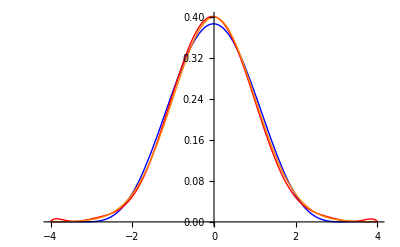

```mathematica
Plot[{f11[x],f11R[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Red,Thin},{Orange,Thin}}]
```

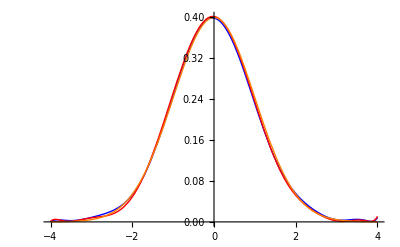

```mathematica
Plot[{f13[x],f13R[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Red,Thin},{Orange,Thin}}]
```

```mathematica
Show[f6[x],f6R[x]]
```

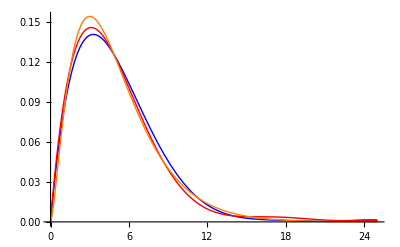

```mathematica
Plot[{f6[x],f6R[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Blue,Thin},{Red,Thin},{Orange,Thin}}]
```

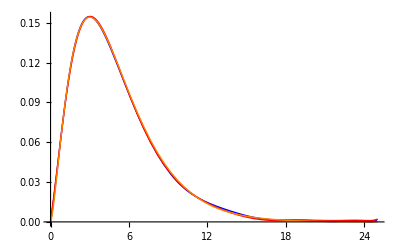

```mathematica
Plot[{f12[x],f12R[x],PDF[ChiSquareDistribution[5],x]},{x,0,25},PlotStyle->{{Blue,Thin},{Red,Thin},{Orange,Thin}}]
```